```mathematica
Integrate[1/π(1/2(1/2))/((1/2(1/2)^2)+(w-(2-2Cos[1Sin[θ]Cos[ϕ]]))^2)Sin[θ],{θ,0,π},{ϕ,0,2π},Assumptions->{r>0}]
```

$Aborted

```mathematica
FullSimplify[1/π(1/2(1/2))/((1/2(1/2)^2)+(w-(2-2Cos[1Sin[θ]Cos[ϕ]]))^2)Sin[θ]]
```

Sin[θ]/(4 π (1/8+(-2+w+2 Cos[Cos[ϕ] Sin[θ]])^2))

```mathematica
FullSimplify[(-128Cos[x]+64+64 Cos[x]^2)^(1/2)]
```

8 √((-1+Cos[x])^2)

```mathematica
(((1.913*2.818)^2)*1.0/(2*π*1.0))*2
```

9.25043

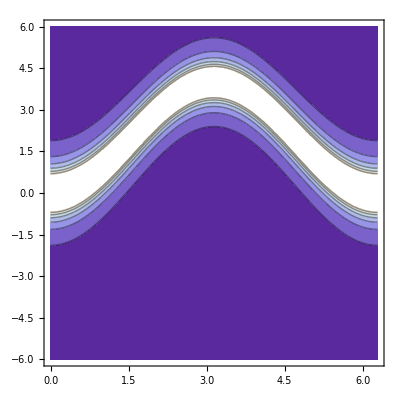

```mathematica
ContourPlot[2*(((1.913*2.818)^2)*1.0/(2*π*1.0))((14.7-(2-2Cos[kx]))/14.7)1/π(1/2(1/2))/((1/2(1/2)^2)+(w-(2-2Cos[kx]))^2),{kx,0,2π},{w,-6,6}]
```

```mathematica
(Exp[(2-2Cos[1])/(8.617343*10^-2*0.0001)]-1)^-1
```

3.665606056×10^-46336

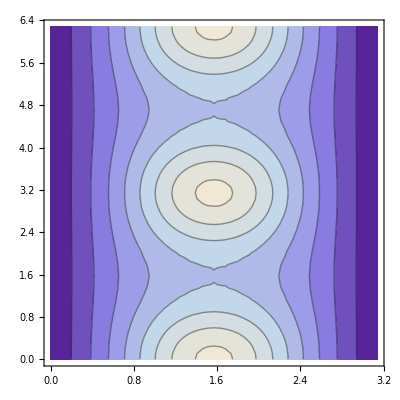

```mathematica
ContourPlot[1/π(1/2(1/2))/((1/2(1/2)^2)+(4-(2-2Cos[1Sin[θ]Cos[ϕ]]))^2)Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

```mathematica
NIntegrate[1/π(1/2(1/2))/((1/2(1/2)^2)+(0-(2-2Cos[1Sin[θ]Cos[ϕ]]))^2)Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

5.04313

```mathematica
2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(2-2Cos[kx]))/14.7)*
```

9.25043

```mathematica
vals=Table[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(2-2Cos[kx]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(w-(2-2Cos[kx]))^2),{w,0,5,.2},{kx,0,π,.2}];
```

```mathematica
2*4/π//N
```

2.54648

```mathematica
Max[vals]
```

23.556

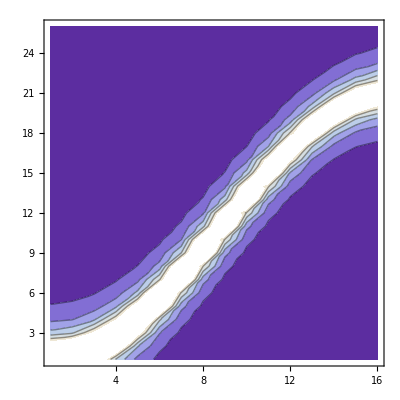

```mathematica
ListContourPlot[vals]
```

```mathematica
lst=Table[NIntegrate[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))(1/(Exp[(2-2Cos[r Sin[θ]Cos[ϕ]])/((8.617343*10^-2)*0.001)]-1))((14.7-(2-2Cos[r Sin[θ]Cos[ϕ]]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(w-(2-2Cos[r Sin[θ]Cos[ϕ]]))^2)r^2 Sin[θ],{θ,0,π},{ϕ,0,2π},Method->{"MonteCarlo"}],{r,0.1,π,π/30},{w,0,5,1/6}]//Quiet
```

{{4661.5,5386.51,2523.05,3721.,630.805,396.214,141.84,4034.24,1292.68,83.4019,24.4375,519.4,49.1992,307.402,175.658,259.413,28.2124,731.555,1103.8,21.9702,36.9993,103.127,29.107,8.50125,283.047,108.449,16.9125,3990.39,68.7744,2.42353,6.02041},{2115.17,31948.,3639.18,5722.51,2609.37,963.979,594.391,417.281,2327.42,992.5,3024.68,178.222,2357.28,1285.17,104.673,14.5814,18.2263,49.5919,30.5948,32.4932,25.1931,41.5537,31.6091,375.252,5.13686,68.0843,518.167,206.354,10.2385,2.73442,6.25444},{5297.23,1067.94,14266.2,290.93,10498.1,1910.09,10796.5,3701.6,12979.3,2194.32,64.0466,6.20706×10^6,135.902,35.0175,164.596,315266.,87.5424,27.7703,2491.98,19.49,93.0161,29.7706,8.5289,8.91714,8.78297,7.04284,196.242,3296.66,43.7718,5.43844,31.3064},{3224.13,1304.82,28419.5,3943.27,596.876,209.447,1635.73,105.672,1232.41,70.7542,42339.3,508.728,1407.12,211.78,2170.71,19365.8,15.042,3372.87,4.1639,71.6745,38746.2,67.3418,55.7684,24.4684,41749.8,40.6236,3824.62,16.662,39.9278,19.7042,29.215},{2359.34,3445.17,5448.06,1261.33,30739.7,495.82,1657.81,111.78,46.8253,931.36,550.914,351.703,11923.2,178.363,42.5318,8035.63,39.2875,606.905,12.9222,53.7665,6.03241,37.4187,107.517,12.489,42.4213,16.8718,4321.05,53.092,8.08706,10.4798,12.9133},{2.87594×10^6,1758.15,9790.86,13577.4,2192.81,32556.3,926.226,135.007,20815.1,326137.,3516.78,810.749,54846.2,6341.36,52.3737,19.9748,15.0515,29.4359,187.822,479.796,6.99063,126.646,944.156,18.2726,13.1185,16.136,12.7821,87.8957,239.195,6.55208,649.674},{20614.6,12224.6,394.754,1593.93,8952.68,187.012,150.491,51.387,745.187,334.758,1642.44,113192.,59.2341,25.9213,39.2527,44.1977,263.613,17.1515,4.4987,7.34201,3.73217,207.777,33.5216,22.4342,20.1523,9.43051,734.698,16.3246,2.14013,2727.03,18.959},{6417.41,1100.42,374.546,23101.8,256.728,244.003,1352.93,8563.4,245.233,477.9,164.487,101.355,81.235,238.087,594.493,15.2948,460.674,168.094,27.677,147.907,81.8387,4.27641,9.3088,254.412,15.3634,3.45944,12.4108,74.3948,3.90557,56.8265,324.572},{4204.65,3271.06,1465.33,2123.49,649.165,1043.82,121.378,129.352,1710.07,5836.75,275.925,705.679,1735.33,13.7016,128.768,35.9072,53.9968,355.963,6.33597,17.3921,184.698,8.29304,176.276,56.4265,5.62137,52.8742,90.2184,19.774,171.163,32.8146,18.7569},{45570.2,60740.4,5094.91,366.089,218.49,206.105,3475.29,161.982,148.102,7.43426×10^6,325.702,293.306,61.2189,25.2571,9218.08,255.559,68.3031,389.324,137.192,1045.92,163.938,120.054,538.371,35.5865,7.82968,6.59075,7243.9,9.53323,192.881,24.3368,35.312},{687.101,4514.15,14787.5,1974.21,395.507,266.34,2762.12,893.808,579.065,709.047,55.0561,44.9201,105.773,72.4674,63.8859,175.686,95942.4,31.6059,79.1692,188.476,204.397,17.1649,29.159,67.0749,33.5529,85.284,3.41771,43.013,35.4157,83.3816,40.647},{8196.03,6884.6,614.833,692.695,301.841,4249.25,175.418,668.117,1073.56,334.855,380092.,68.7,498.997,666.095,86.7213,28.0585,60.199,19.8245,17.0631,63.2637,107.435,7.3996,84.9511,6.32599,403.358,34.8145,31.2269,55.5324,53.569,4.61008,36.5272},{3226.99,8501.31,47738.6,1.87054×10^6,326.84,31976.7,288201.,375.268,665.633,19960.4,181.076,109.459,443.708,27.9555,48.1435,192.811,29.8228,79.0676,32.3198,251.031,122.935,10.1989,20.7078,13.0826,40.5355,18.0716,8.20374,27.0567,32.7075,6.06424,17.6091},{1864.22,1251.59,6340.11,61430.3,1705.48,794.957,1075.51,5541.24,246.141,74612.9,224.296,477.661,1060.4,377.009,2464.47,206.303,76.8162,41.2703,160.773,3891.35,1193.,108.256,195.789,105.286,18.3519,12.0916,293.587,40.2249,35.7906,10.6858,3.95447},{152888.,971.921,1423.36,924.566,1499.35,1404.78,380.664,1014.45,827.33,198.538,253.85,195.404,188.709,117.702,123.089,40.7172,133.766,53.7317,35.5304,1129.33,19.6986,9.09542,16.2385,145.913,9.398,25.5765,31.9089,702.365,13.6625,56.1847,12.8491},{184839.,54320.5,2869.45,6498.5,464.778,486.965,329.167,1858.86,180.443,304.367,507.139,158.665,153.739,110.963,207.68,1220.11,105.464,27.2708,39.3536,131.777,87.606,13.2002,38.0304,14.4673,37.5418,7.89209,11164.,11.075,94.0419,8.66246,6.25193},{1.2005×10^6,12625.7,2685.41,1124.63,457.425,189665.,362.957,353.642,746.814,5181.59,966.942,218.303,197.557,168.351,193.839,92.3832,4287.39,161.559,113.881,242.426,20.648,111.058,53.0906,97.0341,21.3133,518.222,13.6319,195.386,3.10904×10^6,220.812,109.633},{1065.34,2942.18,2380.09,146488.,12804.1,360.191,4130.4,296.901,386.157,217.516,289.162,260.368,1757.87,392.229,147.822,144.533,8787.63,82.9909,90.7759,34.8791,21.2216,78.8441,16.6886,12.3,20.193,13.7253,35.0697,47.5676,121980.,10.456,30.4431},{26237.,15889.9,2037.62,1659.24,4681.49,1324.55,782.014,380.943,428.597,264.596,510.835,246.223,572.312,233.996,26388.3,2064.26,162.873,116.569,68.9009,45.6229,194.872,7087.2,66.7833,105.962,126.434,14.9333,55.3571,34.8266,5883.4,17.4067,10.2182},{3264.73,1893.97,33401.1,10757.1,23100.6,401.211,312.158,391.762,566.345,244.302,244.669,261.483,1070.12,350.297,339.344,6144.17,490.198,178.011,166.77,71.7288,78.647,252.087,34.5884,39.09,1294.48,33.6522,18.1435,18.8208,13.88,22.2033,405.215},{2073.64,25289.7,725.999,7642.05,711.73,831.077,381.527,932.329,1430.73,317.235,11329.3,273.811,248.012,225.512,1676.96,652.532,106207.,199.406,176.03,347.925,72.8313,81.8415,37.3209,40.0573,36.8573,49.6004,25.3972,23.5166,14.7195,12.4779,58.0087},{10364.3,5269.62,7667.58,2368.52,1524.97,1621.1,117076.,356.336,323.041,386.929,466.122,313.672,272.688,249.865,2506.34,224.397,338.548,824.064,266.829,854.797,130.018,84.212,69.5595,149.334,98.4814,30.8367,28.0683,28.9706,45.0094,12.0369,414.453},{200540.,16695.4,8544.72,1347.53,1197.81,693.355,400.371,382.498,2843.27,478.32,277.071,379.529,443.604,240.289,251.864,3552.45,1979.13,240.388,245.738,250.002,186.334,135.865,1181.95,81.6829,178.87,29.8233,1528.12,18.7103,53.1733,44.2637,65.168},{4100.81,965.14,1417.37,594.188,8388.06,474.412,337.376,596.698,571.929,436.725,272.315,331.431,411.77,344.713,263.386,283.542,6716.34,3426.96,730.092,246.168,262.303,275.92,1600.89,440.802,63.3045,509.571,92.088,112729.,1198.65,15.9837,44.0983},{5104.72,19204.9,65172.2,926.264,713.59,4515.1,630.586,352.544,484.191,1526.43,3401.94,2421.85,1432.19,7313.78,255.372,416.606,388.293,264.441,333.43,277.894,382.859,282.,1603.59,985.533,88.251,60.6786,45.2712,104.444,48.7989,30.5338,20.1407},{3165.13,10891.1,9625.22,1650.12,923.877,2443.66,454.993,1555.67,397.322,417.395,303.071,802.422,487.216,317.032,442.178,277.592,270.45,1917.56,272.514,298.664,494.222,289.466,531.085,249.295,657.882,467.96,9655.03,232.741,32.196,805.883,43.461},{944554.,2856.58,1172.41,1213.03,600.805,26354.2,146392.,431.784,11124.,347.317,675.46,2180.38,734.172,372.398,293.855,820.295,371.265,543.491,792.382,3371.43,339.887,930.748,320.738,265.748,190.395,5241.85,70.196,47.4599,111.768,288.078,30.8324},{3423.24,15693.5,1093.94,1406.85,20260.9,991.221,799.991,2621.19,764.037,331.906,664.536,320.548,335.498,334.043,303.214,797.073,322.482,331.16,378.508,318.542,326.682,358.631,374.956,400.478,297.99,254.35,93.3996,62.0117,51.9929,67.6794,83.229},{5.85781×10^6,36941.9,1867.01,1563.72,4214.66,541.351,1579.24,662.816,16240.1,381.257,516.902,359.11,536.266,516.264,131571.,366.116,309.015,381.776,2276.85,517.991,611.233,369.168,436.226,2624.23,2197.08,192.25,121.889,245.596,69.8687,51.7468,590.13},{43856.,8498.36,7223.84,212305.,544.931,597.631,678.147,3747.54,2453.92,602.573,355.603,764.524,584.653,359.046,346.914,316.528,344.069,1903.46,486.902,808.061,377.706,419.28,1396.05,4107.12,399.191,254.696,153.344,106.345,70.2097,278.726,40.0309}}

# ← This is what the plot looks like with the proper form factor: (1/2 g F(κ))^2

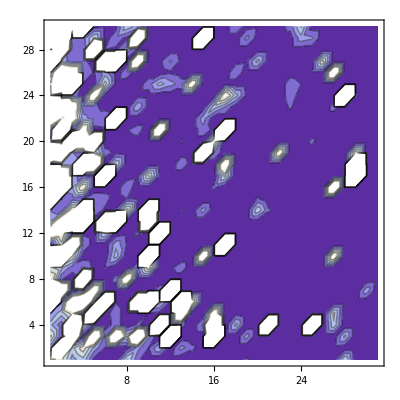

```mathematica
ListContourPlot[lst]
```

```mathematica
{523.344637790916,555.9775801528555,450.06826127053,382.71046461343843,347.73005630451695,325.8338326661845,315.42654257661275,308.86972242582453,316.8065973058143,325.9091444272565,367.1680606203278,425.17102547928755,389.53220933181194,138.88782240241227,62.103054915446,36.40288824724365}-{467.069221453134,519.808010478993,292.322299510204,287.244284529843,338.980954219716,379.727324543641,162.435417988404,36.4186853770459,618.010974246558,315.216512739039,312.100549953185,301.621675124277,394.876533038488,434.581085996050,65.3287841142702,0}
```

{56.2754,36.1696,157.746,95.4662,8.7491,-53.8935,152.991,272.451,-301.204,10.6926,55.0675,123.549,-5.34432,-295.693,-3.22573,36.4029}

```mathematica
lst=Table[NIntegrate[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(2-2Cos[r Sin[θ]Cos[ϕ]]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(0-(2-2Cos[r Sin[θ]Cos[ϕ]]))^2)r^2 Sin[θ],{θ,0,π},{ϕ,0,2π},Method->{"MonteCarlo"}],{r,0,π,π/15}]//Quiet
```

{0.,12.6457,47.5919,91.2251,130.152,167.776,200.727,236.014,275.789,313.843,343.02,383.371,410.599,448.831,495.554,521.856}

```mathematica
lst=Table[NIntegrate[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(2-2Cos[π Sin[θ]Cos[ϕ]]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(w-(2-2Cos[π Sin[θ]Cos[ϕ]]))^2)π^2 Sin[θ],{θ,0,π},{ϕ,0,2π},Method->{"MonteCarlo"}],{w,0,5,1/3}]//Quiet
```

{523.345,555.978,450.068,382.71,347.73,325.834,315.427,308.87,316.807,325.909,367.168,425.171,389.532,138.888,62.1031,36.4029}

```mathematica
((1.913*2.818^2)*1.0/(2*π*1.0))((14.7-(2-2Cos[r Sin[θ]Cos[ϕ]]))/14.7)
```

2.41778